```mathematica
yyy+1/x yy-2y=x^2;
x0=0.5;
yy0=-0.5;
y0=-1;
```

6

{0.5,0.6,0.7,0.8,0.9,1.}

{{},0.,0.133672,0.410138,0.866183,1.54199}

{{},0.8,2.05574,3.66564,5.66096,8.07746}

Print

6

{0.5,0.6,0.7,0.8,0.9,1.}

{{},0.1,0.26435,0.488962,0.786745,1.17213}

{{},1.4,1.94501,2.61196,3.41567,4.37158}

6

{0.5,0.6,0.7,0.8,0.9,1.}

{{},1.,1.02929,1.08829,1.18351,1.32194}

{{},0.177778,0.443022,0.772122,1.16891,1.63845}

1

0

0

-0.5+c1

{{c1→0.5,c2→-3.89899}}

0.5

-3.89899

{{-1.19949,-3.89899,0.5},{-1.43939,-3.83365,0.863012},{-1.67929,-3.72545,1.36857},{-1.91919,-3.55896,2.04037},{-2.15909,-3.31638,2.90212},{-2.39899,-2.97753,3.97753}}

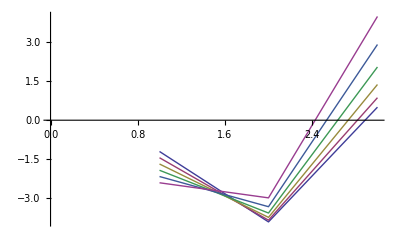

```mathematica
(*n=(b-a)/h+1;*)
solve[f1_,f2_, y0_,z0_] :=(
a=0.5;
b=1;
h = 0.1;
X=Range[a,b,h];
n=Length[X];
Print[n];
Print[X];
Y=Table[{},{n}];
Z=Table[{},{n}];
Y2=Table[{},{n}];
Z2=Table[{},{n}];
Y2[[1]]=y0;
Z2[[1]]=z0;
For[i=2,i≤n,i++,
Y[[i]]=Y2[[i-1]]+h*f1[X[[i-1]],Y2[[i-1]],Z2[[i-1]]];
Z[[i]]=Z2[[i-1]]+h*f2[X[[i-1]],Y2[[i-1]],Z2[[i-1]]];
Y2[[i]]=Y2[[i-1]]+h*(f1[X[[i-1]],Y2[[i-1]],Z2[[i-1]]]+f1[X[[i]],Y[[i]],Z[[i]]])/2;
Z2[[i]]=Z2[[i-1]]+h*(f2[X[[i-1]],Y2[[i-1]],Z2[[i-1]]]+f2[X[[i]],Y2[[i]],Z[[i]]])/2;
];
Print[Y];
Print[Z];
dots=Table[{},{n}];
For[i=1,i≤n,i++,
dots[[i]]={X[[i]],Y2[[i]],Z2[[i]]};
];
(*ListLinePlot[dots]*)
Return[dots];
);

f1[x_,y_,z_]:=z;(*y'*)
f2[x_,y_,z_]:=8+2/x z + 4/(x^2+2)y; (*z'*)
f3[x_,y_,z_]:=2/x z + 4/(x^2+2)y; 
y0=0;
z0=0;
dots1 = solve[f1,f2,y0,z0];
Print
y0=0;
z0=1;
dots2 = solve[f1,f3,y0,z0];
y0=1;
z0=0;
dots3 = solve[f1,f3,y0,z0];
Clear[c1,c2];
eq1 =c1 dots2[[1,3]] + c2 dots3[[1,3]] - 0.5 + dots1[[1,3]];
Print[dots2[[1,3]]];
Print[dots3[[1,3]]];
Print[dots1[[1,3]]];
eq2 = c1(dots2[[6,2]] + dots2[[6,3]]) + c2 (dots3[[6,2]] + dots3[[6,3]]) -( 1 - dots1[[6,2]] - dots1[[6,3]]);
Print[eq1];
l = SolveAlways[eq1==0 && eq2==0, x];
Print[l];
c1 =(c1/.l)[[1]];
Print[c1];
c2 =(c2/.l)[[1]];
Print[c2];
dots = dots1 + c1 * dots2 + c2 * dots3;
Print[dots];
ListLinePlot[dots]
```